{a1→0.197212,b1→0.026941,k1→2.1959,a2→0.334688,b2→0.0393076,k2→3.07105,c→11.7858}

0.137475

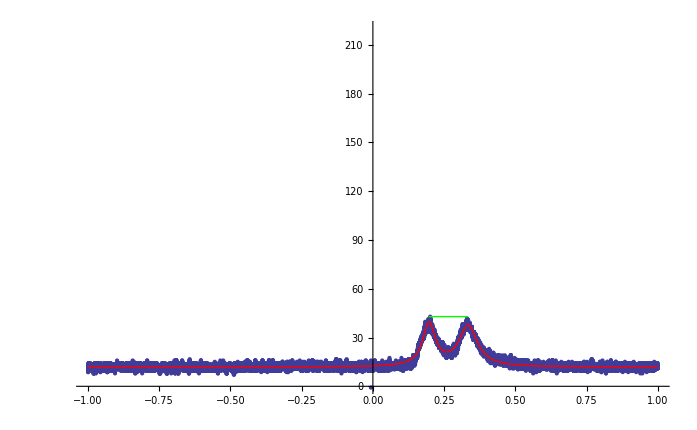

```mathematica
rawData = Import[NotebookDirectory[]<>"mod_abst_88cm.dat"];
messData = ToExpression[rawData];
Clear @ model;
model[x_] =k1/((1+(x-a1)^2/b1^2) b1 π)+k2/((1+(x-a2)^2/b2^2) b2 π) +c;
Peak = Max[messData];
param=FindFit[messData, model[x], {{a1,0.1},{ b1,0.1},{  k1, 18},{ a2,0.3},{  b2,0.1},{  k2,18},{  c,10}}, x]
Distance = a2-a1 /. param
Show[ListPlot[messData, PlotRange->{{-1, 1},{0,  220}}], Plot[model[x]  /. param, {x, -1, 1}, PlotRange->{{-1, 1},{0, 220}}, PlotStyle->Red], Graphics[{Green, Line[{{a1,Peak},{a2,Peak}} /. param]}]]
```

```mathematica
Peak
```

210.303